This script is to explore parameter value sets that render point equilibrium and also, luckily, fit the empirical data well

### Produce time series

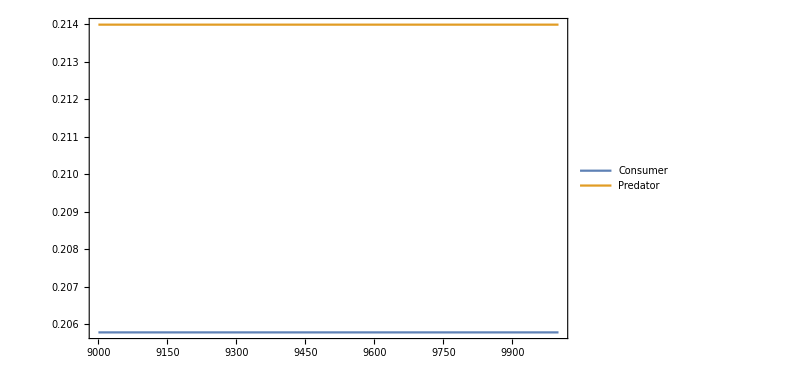

{{0.205778},{0.213988}}

```mathematica
ClearAll["Global`*"];
r1=1.71641*0.15;
K1=8.13829;
r2=1.71641*0.15;
K2=8.13829;
A=1.25;
H=0.08;
B=0.4;
S1=1.25;
h1=0.8;
e1=0.4;
S2=0.38580;
h2=0.35959;
e2=0.4;
M=0.1;
d=0.1;

α=0.;
p=0.04;

Tf = 10000;
eqs={
Res1'[t]==r1*Res1[t]*(1-Res1[t]/K1)-((A*p*Res1[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*(1-p)*Res1[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Res2'[t]==r2*Res2[t]*(1-Res2[t]/K2)-((A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*p*Res2[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Con'[t]==((B*A*p*Res1[t]+B*A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-M*(Con[t])^2-((S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Pred'[t]==((e1*S1*(1-p)*Res1[t]+e1*S1*p*Res2[t]+e2*S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t]-d*(Pred[t])^2,
Res1[0]==1, Res2[0]==1, Con[0]==1, Pred[0]==1};
s = NDSolve[eqs, {Res1,Res2, Con, Pred, q},{t,0,Tf}];
Plot[
Evaluate[{ Con[t],Pred[t]}/.s],
{t,9000,Tf},
PlotStyle->Automatic,
PlotLegends->{"Consumer", "Predator"},
ImageSize->600,
PlotRange->All,
Frame->True]
Table[{Con[t]/.s, Pred[t]/.s}, {t, 9000, 10000, 1}]//Mean
```

```mathematica
Export["D:\\Research\\IGP_LabExp_Public\\TScheck\\TS_e1040_r015_a00.csv",
Join[Table[Flatten[{t, Evaluate[{Res1[t], Res2[t], Con[t], Pred[t]}/.s]}],{t,0,1000}], Table[Flatten[{t, Evaluate[{Res1[t], Res2[t], Con[t], Pred[t]}/.s]}],{t,9000,10000}]]]
```

D:\Research\IGP_LabExp_Public\TScheck\TS_e1040_r015_a00.csv

```mathematica
2
```

#### This second section is to plot model results with fixed e2 and p values but α varying from 0 to 1

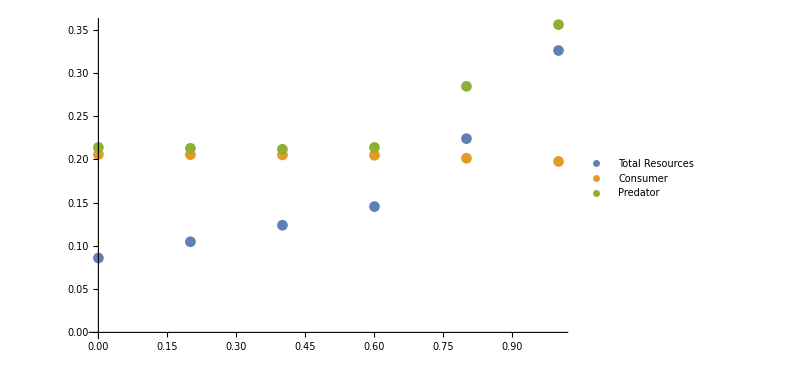

```mathematica
ClearAll["Global`*"];
r1=1.71641*0.15;
K1=8.13829;
r2=1.71641*0.15;
K2=8.13829;
A=1.25;
H=0.08;
B=0.4;
S1=1.25;
h1=0.8;
e1=0.4;
S2=0.38580;
h2=0.35959;
e2=0.4;
M=0.1;
d=0.1;

p = 0.04;

Tf = 10000;
eqs={
Res1'[t]==r1*Res1[t]*(1-Res1[t]/K1)-((A*p*Res1[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*(1-p)*Res1[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Res2'[t]==r2*Res2[t]*(1-Res2[t]/K2)-((A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-((S1*p*Res2[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Con'[t]==((B*A*p*Res1[t]+B*A*(1-p)*Res2[t])/(1+H*A*p*Res1[t]+H*A*(1-p)*Res2[t]))*Con[t]-M*(Con[t])^2-((S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t],
Pred'[t]==((e1*S1*(1-p)*Res1[t]+e1*S1*p*Res2[t]+e2*S2*α*Con[t])/(1+S1*h1*(1-p)*Res1[t]+S1*h1*p*Res2[t]+S2*h2*α*Con[t]))*Pred[t]-d*(Pred[t])^2,
Res1[0]==1, Res2[0]==1, Con[0]==1, Pred[0]==1};

aa = Reap[
Do[
α=i;
sol=NDSolve[eqs, {Res1, Res2,Con, Pred},{t,0,Tf}];
Sow[
{i, Table[{Res1[t]/.sol, Res2[t]/.sol, Con[t]/.sol, Pred[t]/.sol}, {t, 8000, 10000, 0.1}]//Mean}
];
,{i, 0,1, 0.2}
]
][[2,1]];
ListPlot[
{Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]]+aa[[n]][[2]][[2]][[1]]}, {n,1, 6}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[3]][[1]]},  {n,1, 6}],
Table[{aa[[n]][[1]], aa[[n]][[2]][[4]][[1]]},  {n,1, 6}]},
PlotLegends->{"Total Resources", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All
]
(*MatrixForm[Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]], aa[[n]][[2]][[2]][[1]], aa[[n]][[2]][[3]][[1]], aa[[n]][[2]][[4]][[1]]}, {n,1, 21}]]*)
```

### This section is to save the results with fixed e2 and p values but α varying from 0 to 1

```mathematica
aa = Reap[
Do[
α=i;
sol=NDSolve[eqs, {Res1, Res2,Con, Pred},{t,0,Tf}];
Sow[
{i, Table[{Res1[t]/.sol, Res2[t]/.sol, Con[t]/.sol, Pred[t]/.sol}, {t, 8000, 10000, 0.01}]//Mean}
];
,{i, 0,1, 0.2}
]
][[2,1]];
Export["D:\\Research\\IGP_LabExp_Public\\Type2ModResults_R\\Type2_e1040_r015.csv",Table[{aa[[n]][[1]], aa[[n]][[2]][[1]][[1]], aa[[n]][[2]][[2]][[1]], aa[[n]][[2]][[3]][[1]], aa[[n]][[2]][[4]][[1]]}, {n,1, 6}]];
```